# Числено диференциране

## Параметрите a и b са съответно предпоследната и последната цифра от факултетния номер

1. Да се състави таблицата (x_m, ψ(x_m)),, където
x_m = −b + m(0.2), m = OverBar[1, 6] ,         ψ(x) = ((a+1)x - 2)/(x^2 + 1)
2. Да се намерят първите производни ψ_j',  j = OverBar[1, 6]
3. Да се намерят вторите производни ψ_j'',  j = OverBar[2, 5]

## Генериране на данни

```mathematica
xt = Table[-7 + m *0.2, {m, 1,6}]
```

{-6.8,-6.6,-6.4,-6.2,-6.,-5.8}

```mathematica
f[x_] := (7x - 2)/(x^2 + 1)
yt = f[xt]
```

{-1.04996,-1.08169,-1.11535,-1.15112,-1.18919,-1.22979}

```mathematica
h = 0.2
```

0.2

```mathematica
n = Length[xt]
```

6

## Формули с точност O(h^2) - втори порядък

### Първа производна

Попълваме средните точки

```mathematica
yp2 = Table[(yt[[i+1]] - yt[[i-1]])/(2h), {i, 2, n - 1}]
```

{-0.163476,-0.17357,-0.184603,-0.196691}

Допълваме производната в десния край (последната)

```mathematica
AppendTo[yp2, (yt[[n - 2]] - 4yt[[n-1]] + 3yt[[n]])/(2h)]
```

{-0.163476,-0.17357,-0.184603,-0.196691,-0.209338}

Допълваме производната в левия край (първата)

```mathematica
PrependTo[yp2, (-3yt[[1]] +4yt[[2]] - yt[[3]])/(2h)]
```

{-0.153824,-0.163476,-0.17357,-0.184603,-0.196691,-0.209338}

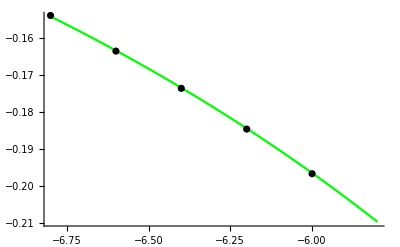

```mathematica
pointsyp2 = Table[{xt[[i]], yp2[[i]]}, {i , 1, n-1}] ;
gryp2 = ListPlot[pointsyp2, PlotStyle->Black];
grfyp = Plot[f'[x], {x, xt[[1]], xt[[n]]}, PlotStyle->Green];
Show[grfyp, gryp2]
```

### Втора производна

Попълваме средните точки

```mathematica
ypp2 = Table[(yt[[i+1]] -2 yt[[i]]+yt[[i-1]])/h^2, {i, 2, n - 1}]
```

{-0.0482597,-0.0526833,-0.0576476,-0.0632347}

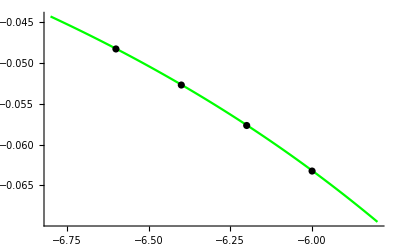

```mathematica
pointsypp2 = Table[{xt[[i + 1]], ypp2[[i]]}, {i , 1, n-2}] ;
grypp2 = ListPlot[pointsypp2, PlotStyle->Black];
grfypp = Plot[f''[x], {x, xt[[1]], xt[[n]]}, PlotStyle->Green];
Show[grfypp, grypp2]
```